## Comparison of different vehicle models

### Import Data & Equations

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Antonio\Desktop\Single-Track-Vehicle-Model

```mathematica
parameters=ChoiceDialog["Please select the car parameters",
FileNames["Car_Parameters/*.json"]]
```

Car_Parameters\test.json

```mathematica
data=ToExpression[TextString[Import[parameters,"JSON"]]];
```

```mathematica
dataG={
l->a1+a2,
μ->mu,
qb->((a2*q1+a1*q2)/(a1+a2)),
δ10->delta10*(Pi/180),
δ20->delta20*(Pi/180),
τ1->tau1,τ2->tau2,
ϵ1->epsilon1,ϵ2->epsilon2,
ρ->rho,
kϕ1->kphi1,kϕ2->kphi2,
kϕ->kphi1+kphi2,
kϕ1p->kphi1p,kϕ2p->kphi2p,
kϕp->kphi1p+kphi2p,
kϕ1s->kphi1s,kϕ2s->kphi2s,
kϕs->kphi1s+kphi2s,
Jz->m*a1*a2*0.92
}/.data;
```

```mathematica
traction=ToString@Extract[Association[data],Key@Traction]
```

rear

```mathematica
keyList ={{Key@delta10},{Key@delta20},
{Key@tau1},{Key@tau2},{Key@epsilon1},
{Key@epsilon2},{Key@rho},{Key@kphi1},
{Key@kphi2},{Key@kphi1p},{Key@kphi2p},
{Key@Traction},{Key@kphi1s},{Key@kphi2s}};
```

```mathematica
param=Normal@Thread[Delete[Association[Join[data,dataG]],keyList]]
```

{m→1464,g→9.81,a1→1.13,a2→1.47,t1→1.6,t2→1.6,h→0.55,rr1→0.25,rr2→0.25,mu→1.4,a1mf→-0.00005,a2mf→1,a3mf→55000,a4mf→4000,ya→0.8,xm→0.08,Sa→2,Cx→0.35,Cz1→0.,Cz2→0.,Jzx→10,q1→0.05,q2→0.05,k1→31500,k2→28000,c1→2948.4,c2→2620.8,l→2.6,μ→1.4,qb→0.05,δ10→0.,δ20→0.,τ1→0.05,τ2→0.,ϵ1→1.,ϵ2→0.,ρ→1.225,kϕ1→50000,kϕ2→40000,kϕ→90000,kϕ1p→400,kϕ2p→500,kϕp→900,kϕ1s→21740.6,kϕ2s→22322.2,kϕs→44062.8,Jz→2237.3}

#### Import Equations

```mathematica
NotebookEvaluate/@FileNames["Equations.nb",NotebookDirectory[]];
```

#### Draw

```mathematica
drawDouble[values_, title_, xlabel_, ylabel_,tf_]:=
Plot[values/.param,{t,0,tf},
PlotRange->All,
Filling->Automatic,
AspectRatio->1/4.0,
FrameLabel->{HoldForm[xlabel],HoldForm[ylabel]},
PlotLabel->HoldForm[title],
LabelStyle->Directive[Bold],
ImageSize->650,
PlotStyle->Thickness[0.0024],
GridLines->{None, Automatic},
Frame->True,
RotateLabel->False,
GridLinesStyle->{{Gray, Dotted}, {Black, Dotted}}]
```

```mathematica
ColorData[97, "ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
orange = ColorData[97, "ColorList"][[2]]
```

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
red = ColorData[3, "ColorList"][[2]]
```

RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862]

```mathematica
blue = ColorData[97, "ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
green = ColorData[97, "ColorList"][[3]]
```

RGBColor[0.560181, 0.691569, 0.194885]

# Car Models

#### Input for

```mathematica
tf=800;
```

```mathematica
u[t_]:=25;
```

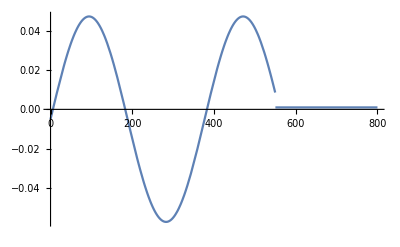

```mathematica
δv[t_]:=Which[
t≤550,3*Degree*(Sin[t/60])-0.005,
t>550,0.001]
Plot[Evaluate[δv[t]],{t,0,tf}]
```

### Double Track Model

```mathematica
eqnsDouble[u_,v_,r_,up_,vp_,rp_,ω11_,ω12_,ω21_,ω22_,δv_]:={
Fx21[u,v,r,ω21,up,vp,δv]-Fx22[u,v,r,ω22,up,vp,δv]==0,
ω11-V11w[u,v,r,δv][[1]]/rr1==0,
ω12-V12w[u,v,r,δv][[1]]/rr1==0,
Jz*rp-Nm[u,v,r,up,vp,δv,ω11,ω12,ω21,ω22]==0,
X[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ax[up,v,r]==0,
Y[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ay[vp,u,r]==0
}/.param
```

#### Initial conditions

```mathematica
initialConditionsDouble[u_?NumericQ,δv_?NumericQ]:=
FindRoot[{
eqnsDouble[u,v0,r0,0,0,0,ω110,ω120,ω210,ω220,δv]},
{{v0,0.0001},{r0,0.0001},
{ω110,((u/rr1-0.25))},{ω120,((u)/rr1+0.25)},
{ω210,((u)/rr2-0.25)},{ω220,(u/rr2+0.25)}
}/.param
]
```

```mathematica
icDouble=initialConditionsDouble[u[0],δv[0]]
```

{v0→0.00397402,r0→-0.00175231,ω110→100.006,ω120→99.9944,ω210→100.257,ω220→100.247}

```mathematica
param
```

{m→1464,g→9.81,a1→1.13,a2→1.47,t1→1.6,t2→1.6,h→0.55,rr1→0.25,rr2→0.25,mu→1.4,a1mf→-0.00005,a2mf→1,a3mf→55000,a4mf→4000,ya→0.8,xm→0.08,Sa→2,Cx→0.35,Cz1→0.,Cz2→0.,Jzx→10,q1→0.05,q2→0.05,k1→31500,k2→28000,c1→2948.4,c2→2620.8,l→2.6,μ→1.4,qb→0.05,δ10→0.,δ20→0.,τ1→0.05,τ2→0.,ϵ1→1.,ϵ2→0.,ρ→1.225,kϕ1→50000,kϕ2→40000,kϕ→90000,kϕ1p→400,kϕ2p→500,kϕp→900,kϕ1s→21740.6,kϕ2s→22322.2,kϕs→44062.8,Jz→2237.3}

#### Integration

```mathematica
DoubleModel[u_,δv_,ts_]:=First@NDSolve[{
eqnsDouble[u,vn[t],rn[t],u'[t],vn'[t],rn'[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],δv],
vn[0]==v0,
rn[0]==r0,
ω11n[0]==ω110,
ω12n[0]==ω120,
ω21n[0]==ω210,
ω22n[0]==ω220
}/.icDouble,
{vn[t],rn[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t]},
{t,0,tf},
AccuracyGoal->8,PrecisionGoal->8
]
```

```mathematica
solDouble=DoubleModel[u[t],δv[t],tf]
```

{vn[t]→InterpolatingFunction[…][t],rn[t]→InterpolatingFunction[…][t],ω11n[t]→InterpolatingFunction[…][t],ω12n[t]→InterpolatingFunction[…][t],ω21n[t]→InterpolatingFunction[…][t],ω22n[t]→InterpolatingFunction[…][t]}

#### States definition

```mathematica
vD[t_]:=vn[t]/.solDouble;
```

```mathematica
rD[t_]:=rn[t]/.solDouble;
```

```mathematica
ω11D[t_]:=ω11n[t]/.solDouble;
```

```mathematica
ω12D[t_]:=ω12n[t]/.solDouble;
```

```mathematica
ω21D[t_]:=ω21n[t]/.solDouble;
```

```mathematica
ω22D[t_]:=ω22n[t]/.solDouble;
```

```mathematica
ψeqD=NDSolve[{ψsol'[t]==rD[t],ψsol[0]==0},ψsol,{t,0,tf}];
```

```mathematica
ψD[t_]:=First[ψsol[t]/.ψeqD];
```

#### Partial results

```mathematica
xgeq=NDSolve[{xgsol'[t]==u[t]*Cos@ψD[t]-vD[t]*Sin@ψD[t],xgsol[0]==0},xgsol,{t,0,tf}];
```

```mathematica
ygeq=NDSolve[{ygsol'[t]==u[t]*Sin@ψD[t]+vD[t]*Cos@ψD[t],ygsol[0]==0},ygsol,{t,0,tf}];
```

```mathematica
xD[t_]:=First[xgsol[t]/.xgeq]
```

```mathematica
yD[t_]:=First[ygsol[t]/.ygeq]
```

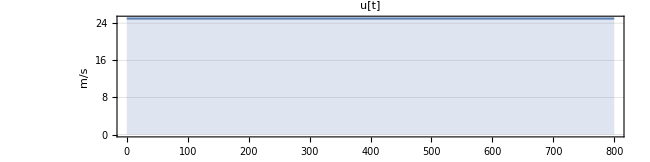
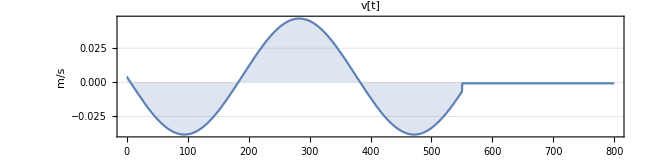
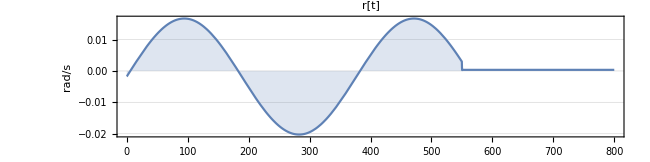
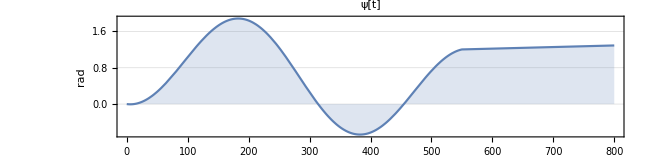

```mathematica
Row[{
drawDouble[u[t],"u[t]","time [s]", "m"/"s",tf],
drawDouble[vD[t],"v[t]","time [s]", "m"/"s",tf],
drawDouble[rD[t],"r[t]","time [s]", "rad"/"s",tf],
drawDouble[ψD[t],"ψ[t]","time [s]", "rad",tf]
}]
```

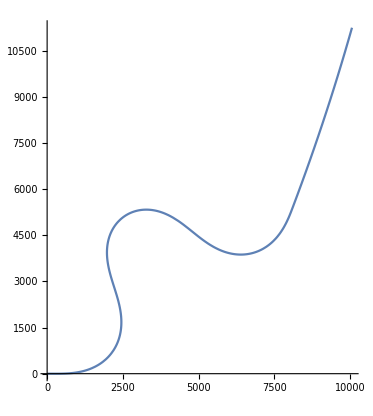

```mathematica
ParametricPlot[
{xD[t],yD[t]},{t,0,tf},
AspectRatio->Automatic,PlotRange->All,
AspectRatio->Automatic,PlotStyle->blue]
```

```mathematica
Manipulate[
ParametricPlot[{{xD[t],yD[t]}},{t,1,x-1},ImageSize->400],
{x,1,tf,Appearance->"Open",AnimationRate->50}]
```

### Single Track Model

#### Single Track Parameters

```mathematica
dataST={
l->a1+a2,
μ->mu,
qb->((a2*q1+a1*q2)/(a1+a2)),
δ10->0,
δ20->0,
τ1->tau1,τ2->tau2,
ϵ1->0,ϵ2->0,
ρ->rho,
kϕ1->kphi1,kϕ2->kphi2,
kϕ->kphi1+kphi2,
kϕ1p->kphi1p,kϕ2p->kphi2p,
kϕp->kphi1p+kphi2p,
kϕ1s->kphi1s,kϕ2s->kphi2s,
kϕs->kphi1s+kphi2s,
Jz->m*a1*a2*0.92
}/.data;
```

```mathematica
keySingleTrack ={{Key@delta10},{Key@delta20},
{Key@tau1},{Key@tau2},{Key@epsilon1},
{Key@epsilon2}};
```

```mathematica
paramST=Normal@Thread[Delete[Association[Join[data,dataST]],keySingleTrack]];
```

```mathematica
uAC=20;
rAC=1;
vAC=1;
```

#### Compute ΔZi

```mathematica
η1=(ΔZ1[0,uAC,rAC]/Y1[0,uAC,rAC] )*(a2/l);
η2=(ΔZ2[0,uAC,rAC]/Y2[0,uAC,rAC] )*(a1/l);
```

```mathematica
Yi[αij_,ΔZi_,Zi0_]:=
(Ft[αij,Zi0+ΔZi]+Ft[αij,Zi0-ΔZi])/.paramST;
```

```mathematica
computeΔZi[αi_,Zi0_,ai_,ηi_,initCond_]:=
FindRoot[{Yi[αi,ΔZi,Zi0]-(ΔZi*ai)/(ηi*l)}/.paramST,
{ΔZi,initCond},
AccuracyGoal->5,
PrecisionGoal->5]
```

```mathematica
αiAC=Range[-0.2,0.2,0.01];
```

```mathematica
(* Compute ΔZ1 *)
```

```mathematica
ΔZ1AC={};
AppendTo[ΔZ1AC,computeΔZi[αiAC[[1]],Z10,a1,η1,-2000][[1,2]]];
For[i=2,i≤Length@αiAC,i++,
AppendTo[ΔZ1AC,computeΔZi[αiAC[[i]],Z10,a1,η1,ΔZ1AC[[i-1]]][[1,2]]];
]
```

```mathematica
(* Compute ΔZ2 *)
```

```mathematica
ΔZ2AC={};
AppendTo[ΔZ2AC,computeΔZi[αiAC[[1]],Z20,a2,η2,-2000][[1,2]]];
For[i=2,i≤Length@αiAC,i++,
AppendTo[ΔZ2AC,computeΔZi[αiAC[[i]],Z20,a2,η2,ΔZ2AC[[i-1]]][[1,2]]];
]
```

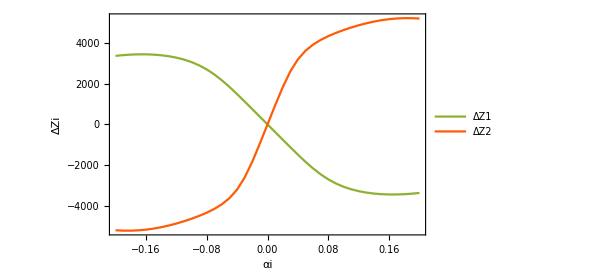

```mathematica
ListLinePlot[{Transpose[{αiAC,ΔZ1AC}],Transpose[{αiAC,ΔZ2AC}]},
PlotRange->All,PlotLegends->{"ΔZ1","ΔZ2"},ImageSize->450,
LabelStyle->Directive[Bold,10],AxesLabel->{"αi","ΔZi"},
PlotStyle->{green,red},Frame->True
]
```

#### Axle Characteristic

```mathematica
Y1AC=Yi[αiAC,ΔZ1AC,Z10]/.paramST;
```

```mathematica
Y2AC=Yi[αiAC,ΔZ2AC,Z20]/.paramST;
```

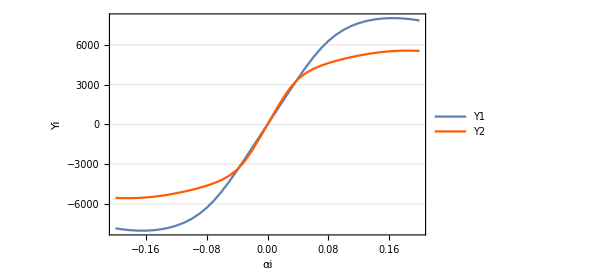

```mathematica
ListLinePlot[{Transpose[{αiAC,Y1AC}],Transpose[{αiAC,Y2AC}]},LabelStyle->Directive[Bold,11],AxesLabel->{"αi","Yi"},
PlotRange->All,PlotLegends->{"Y1","Y2"},ImageSize->450,LabelStyle->Directive[Bold,11],
PlotStyle->{blue,red},Frame->True,GridLines->{None,Automatic},GridLinesStyle->{Dotted,Dotted}]
```

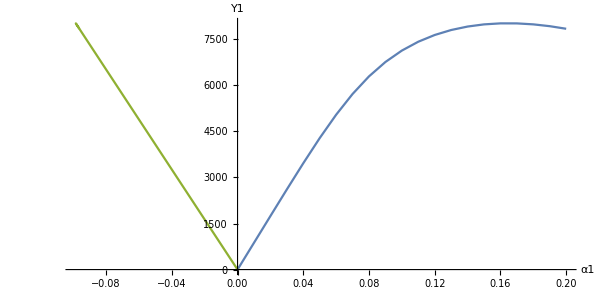
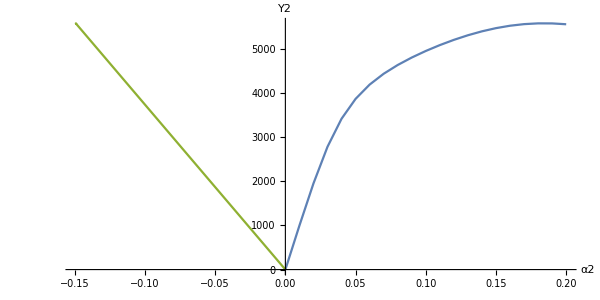

```mathematica
Row[{
ListLinePlot[{
Transpose[{αiAC[[21;;41]],Y1AC[[21;;41]]}],
Transpose[{ΔZ1AC[[21;;41]]/35000,Y1AC[[21;;41]]}]},
AspectRatio->1/2,ImageSize->600,AxesLabel->{"α1","Y1"},
PlotStyle->{blue,green,Bold}],
ListLinePlot[{
Transpose[{αiAC[[21;;41]],Y2AC[[21;;41]]}],
Transpose[{-ΔZ2AC[[21;;41]]/35000,Y2AC[[21;;41]]}]},
AspectRatio->1/2,ImageSize->600,AxesLabel->{"α2","Y2"},
PlotStyle->{blue,green,Bold}]
}]
```

```mathematica
ΔZ1AC[[21;;41]]
```

{0.,-374.563,-748.894,-1121.39,-1487.69,-1839.8,-2166.62,-2456.91,-2703.34,-2904.6,-3064.29,-3188.28,-3282.51,-3351.98,-3400.47,-3430.78,-3444.94,-3444.57,-3431.,-3405.51,-3369.35}

```mathematica
ΔZ2AC[[21;;41]]
```

{0.,933.018,1827.16,2605.46,3199.97,3621.86,3924.77,4154.72,4340.61,4498.87,4638.23,4762.81,4874.04,4971.75,5055.04,5122.76,5173.88,5207.69,5223.95,5222.86,5205.08}

```mathematica
Manipulate[
Column[{
Grid[{{" α1   -> ", αiAC[[x]]},{" ΔZ1  -> ",-ΔZ1AC[[x]]},
{" Y1   -> ",Y1AC[[x]]}},Alignment->Center,Background->{{{None},LightBlue}}],
ListLinePlot[{
Transpose[{αiAC[[21;;41]],Y1AC[[21;;41]]}],
Transpose[{αiAC[[21;;x]],Y1AC[[21;;x]]}],
Transpose[{ΔZ1AC[[21;;41]]/35000,Y1AC[[21;;41]]}],
Transpose[{ΔZ1AC[[21;;x]]/35000,Y1AC[[21;;x]]}]},
AspectRatio->1/2,ImageSize->700,
PlotStyle->{{blue,Dashed,Thickness[0.004]},{Red,Thickness[0.005]} ,
{green,Dashed,Thickness[0.004]},{Red,Thickness[0.005]}},
AxesLabel->{"α1","Y1"},LabelStyle->Directive[Bold,10.6]]}],
{x,21,41,1}]
```

#### SingleTrack Equations

```mathematica
magicFormula=
Dst*Sin[Cst*ArcTan[Bst*x-Est*(Bst*x-ArcTan[Bst*x])]];
```

```mathematica
mf1=FindFit[Transpose[{αiAC,Yi[αiAC,ΔZ1AC,Z10]}]/.paramST,magicFormula,{Bst,Cst,Dst,Est},x]
```

{Bst→7.4721,Cst→1.4809,Dst→7995.19,Est→-1.70226}

```mathematica
mf2=FindFit[Transpose[{αiAC,Yi[αiAC,ΔZ2AC,Z20]}]/.paramST,magicFormula,{Bst,Cst,Dst,Est},x]
```

{Bst→16.8706,Cst→1.05596,Dst→5996.44,Est→0.537587}

```mathematica
Y1SingleTrack[α1_]:=
Dst*Sin[Cst*ArcTan[Bst*α1-Est*(Bst*α1-ArcTan[Bst*α1])]]/.mf1;
```

```mathematica
Y2SingleTrack[α2_]:=
Dst*Sin[Cst*ArcTan[Bst*α2-Est*(Bst*α2-ArcTan[Bst*α2])]]/.mf2;
```

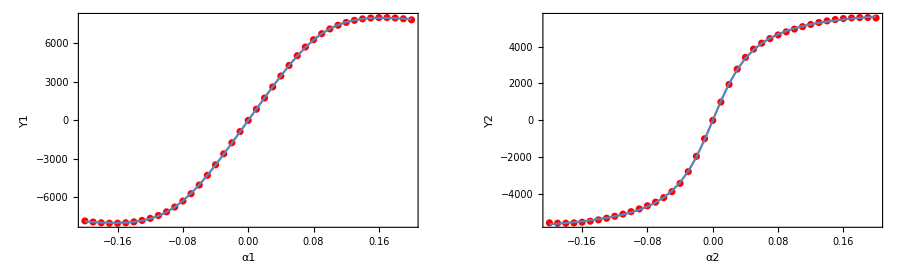

```mathematica
GraphicsRow[ {
Show[ListPlot[{Transpose[{αiAC,Yi[αiAC,ΔZ1AC,Z10]}]},PlotStyle->{Red}],
ListLinePlot[{Transpose[{αiAC,Y1SingleTrack[αiAC]}]}],AxesLabel->{"α1","Y1"},Frame->True],
Show[ListPlot[{Transpose[{αiAC,Yi[αiAC,ΔZ2AC,Z20]}]},PlotStyle->{Red}],
ListLinePlot[{Transpose[{αiAC,Y2SingleTrack[αiAC]}]}],AxesLabel->{"α2","Y2"},Frame->True]
},ImageSize->900]
```

#### Initial Conditions

```mathematica
eqnsSingle[u_,v_,r_,up_,vp_,rp_,ω11_,ω12_,ω21_,ω22_,α1_,α2_,δv_]:={
α1-δv*τ1+(v+r*a1)/u==0,
α2-δv*τ2+(v-r*a2)/u==0,
ω11-V11w[u,v,r,δv][[1]]/rr1==0,
ω12-V12w[u,v,r,δv][[1]]/rr1==0,
Fx21[u,v,r,ω21,up,vp,δv]-Fx22[u,v,r,ω22,up,vp,δv]==0,
X[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ax[up,v,r]==0,
Jz*rp-Y1SingleTrack[α1]*a1+Y2SingleTrack[α2]*a2==0,
Y1SingleTrack[α1]+Y2SingleTrack[α2]-m*ay[vp,u,r]==0
}/.paramST
```

```mathematica
initialConditionsSingle[u_?NumericQ,δv_?NumericQ]:=
FindRoot[{
eqnsSingle[u,v0,r0,0,0,0,ω110,ω120,ω210,ω220,α10,α20,δv]},
{{v0,0.0001},{r0,0.0001},
{ω110,((u/rr1-0.25))},{ω120,((u)/rr1+0.25)},
{ω210,((u)/rr2-0.25)},{ω220,(u/rr2+0.25)},
{α10,0.001},{α20,0.001}
}/.paramST
]
```

```mathematica
icSingle=initialConditionsSingle[u[0],δv[0]]
```

{v0→0.0029799,r0→-0.00132281,ω110→100.004,ω120→99.9958,ω210→100.256,ω220→100.248,α10→-0.000309405,α20→-0.000196977}

#### NDSolve

```mathematica
solModelSingle[u_,δv_,ts_]:=First@NDSolve[{
eqnsSingle[u,vn[t],rn[t],u'[t],vn'[t],rn'[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],α1n[t],α2n[t],δv],
vn[0]==v0,
rn[0]==r0,
ω11n[0]==ω110,
ω12n[0]==ω120,
ω21n[0]==ω210,
ω22n[0]==ω220,
α1n[0]==α10,
α2n[0]==α20
}/.icSingle,
{vn[t],rn[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],α1n[t],α2n[t]},
{t,0,ts},AccuracyGoal->8,PrecisionGoal->8
]
```

```mathematica
solSingle=solModelSingle[u[t],δv[t],tf];
```

#### State Definition

```mathematica
vS[t_]:=vn[t]/.solSingle;
```

```mathematica
rS[t_]:=rn[t]/.solSingle;
```

```mathematica
ω11S[t_]:=ω11n[t]/.solSingle;
```

```mathematica
ω12S[t_]:=ω12n[t]/.solSingle;
```

```mathematica
ω21S[t_]:=ω21n[t]/.solSingle;
```

```mathematica
ω22S[t_]:=ω22n[t]/.solSingle
```

```mathematica
ψeqS=NDSolve[{ψsol'[t]==rS[t],ψsol[0]==0},ψsol,{t,0,tf}];
```

```mathematica
ψS[t_]:=First[ψsol[t]/.ψeqS];
```

#### Plot

```mathematica
xgeqS=NDSolve[{xgsol'[t]==u[t]*Cos@ψS[t]-vS[t]*Sin@ψS[t],xgsol[0]==0},xgsol,{t,0,tf}];
```

```mathematica
ygeqS=NDSolve[{ygsol'[t]==u[t]*Sin@ψS[t]+vS[t]*Cos@ψS[t],ygsol[0]==0},ygsol,{t,0,tf}];
```

```mathematica
xS[t_]:=First[xgsol[t]/.xgeqS]
```

```mathematica
yS[t_]:=First[ygsol[t]/.ygeqS]
```

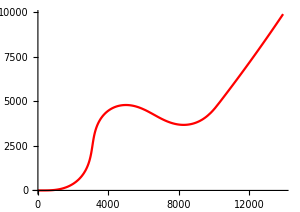

```mathematica
ParametricPlot[{{xS[t],yS[t]}},{t,0,tf},
AspectRatio->Automatic,PlotRange->All,
ImageSize->300,PlotStyle->Red]
```

```mathematica
Manipulate[
ParametricPlot[{{xS[t],yS[t]}},{t,1,x-1},ImageSize->400],
{x,1,tf,Appearance->"Open",AnimationRate->50}]
```

### Linear Single Track

#### Linearization

```mathematica
linear1=FindFit[Transpose[{{0,1*(Pi/180)}, {0,Y1SingleTrack[1*(Pi/180)]}}],C1*xf,C1,xf]
```

{C1→88249.3}

```mathematica
linear2=FindFit[Transpose[{{0,1*(Pi/180)}, {0,Y2SingleTrack[1*(Pi/180)]}}],C2*xf,C2,xf]
```

{C2→100924.}

```mathematica
Y1Linear[α1_]:=C1*α1/.linear1
```

```mathematica
Y2Linear[α2_]:=C2*α2/.linear2
```

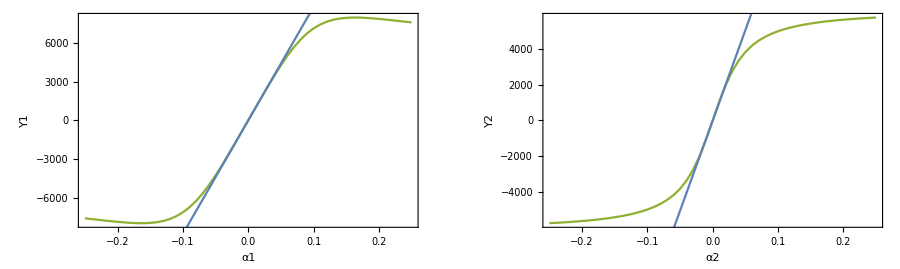

```mathematica
GraphicsRow[{
Show[ListLinePlot[Transpose[{Range[-0.25,0.25,0.01],Table[Y1SingleTrack[α1],{α1,-0.25,0.25,0.01}]}],PlotStyle->green],
ListLinePlot[Transpose[{Range[-0.25,0.25,0.01],Table[Y1Linear[α1],{α1,-0.25,0.25,0.01}]}],PlotRange->All],AxesLabel->{"α1","Y1"},Frame->True],
Show[ListLinePlot[Transpose[{Range[-0.25,0.25,0.01],Table[Y2SingleTrack[α2],{α2,-0.25,0.25,0.01}]}],PlotStyle->green],
ListLinePlot[Transpose[{Range[-0.25,0.25,0.01],Table[Y2Linear[α2],{α2,-0.25,0.25,0.01}]}],PlotRange->All],AxesLabel->{"α2","Y2"},Frame->True]
},ImageSize->900]
```

```mathematica
eqnsLinear[u_,v_,r_,up_,vp_,rp_,ω11_,ω12_,ω21_,ω22_,α1_,α2_,δv_]:={
α1-δv*τ1+(v+r*a1)/u==0,
α2-δv*τ2+(v-r*a2)/u==0,
ω11-V11w[u,v,r,δv][[1]]/rr1==0,
ω12-V12w[u,v,r,δv][[1]]/rr1==0,
Fx21[u,v,r,ω21,up,vp,δv]-Fx22[u,v,r,ω22,up,vp,δv]==0,
X[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ax[up,v,r]==0,
Jz*rp-Y1Linear[α1]*a1+Y2Linear[α2]*a2==0,
Y1Linear[α1]+Y2Linear[α2]-m*ay[vp,u,r]==0
}/.paramST
```

```mathematica
initialConditionsLinear[u_?NumericQ,δv_?NumericQ]:=
FindRoot[{
eqnsLinear[u,v0,r0,0,0,0,ω110,ω120,ω210,ω220,α10,α20,δv]},
{{v0,0.0001},{r0,0.0001},
{ω110,((u/rr1-0.25))},{ω120,((u)/rr1+0.25)},
{ω210,((u)/rr2-0.25)},{ω220,(u/rr2+0.25)},
{α10,0.001},{α20,0.001}
}/.paramST
]
```

```mathematica
icLinear=initialConditionsLinear[u[0],δv[0]]
```

{v0→0.0034145,r0→-0.0013822,ω110→100.004,ω120→99.9956,ω210→100.256,ω220→100.248,α10→-0.000324104,α20→-0.000217853}

#### NDSolve

```mathematica
solModelLinear[u_,δv_,ts_]:=First@NDSolve[{
eqnsLinear[u,vn[t],rn[t],u'[t],vn'[t],rn'[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],α1n[t],α2n[t],δv],
vn[0]==v0,
rn[0]==r0,
ω11n[0]==ω110,
ω12n[0]==ω120,
ω21n[0]==ω210,
ω22n[0]==ω220,
α1n[0]==α10,
α2n[0]==α20
}/.icLinear,
{vn[t],rn[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],α1n[t],α2n[t]},
{t,0,ts},AccuracyGoal->8,PrecisionGoal->8
]
```

```mathematica
solLinear=solModelLinear[u[t],δv[t],tf];
```

#### State Definition

```mathematica
vL[t_]:=vn[t]/.solLinear;
```

```mathematica
rL[t_]:=rn[t]/.solLinear;
```

```mathematica
ω11L[t_]:=ω11n[t]/.solLinear;
```

```mathematica
ω12L[t_]:=ω12n[t]/.solLinear;
```

```mathematica
ω21L[t_]:=ω21n[t]/.solLinear;
```

```mathematica
ω22L[t_]:=ω22n[t]/.solLinear
```

```mathematica
ψeqL=NDSolve[{ψsol'[t]==rL[t],ψsol[0]==0},ψsol,{t,0,tf}];
```

```mathematica
ψL[t_]:=First[ψsol[t]/.ψeqL];
```

#### Plot

```mathematica
xgeqL=NDSolve[{xgsol'[t]==u[t]*Cos@ψL[t]-vL[t]*Sin@ψL[t],xgsol[0]==0},xgsol,{t,0,tf}];
```

```mathematica
ygeqL=NDSolve[{ygsol'[t]==u[t]*Sin@ψL[t]+vL[t]*Cos@ψL[t],ygsol[0]==0},ygsol,{t,0,tf}];
```

```mathematica
xL[t_]:=First[xgsol[t]/.xgeqL]
```

```mathematica
yL[t_]:=First[ygsol[t]/.ygeqL]
```

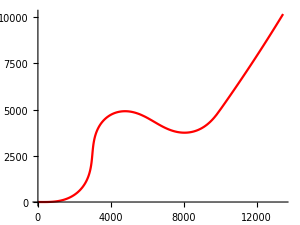

```mathematica
ParametricPlot[{{xL[t],yL[t]}},{t,0,tf},
AspectRatio->Automatic,PlotRange->All,
ImageSize->300,PlotStyle->Red]
```

```mathematica
Manipulate[
ParametricPlot[{{xL[t],yL[t]},{xS[t],yS[t]}},{t,1,x-1},
ImageSize->400,PlotLegends->{"SingleTrack","LinearSingTrack"}],
{x,1,tf,Appearance->"Open",AnimationRate->50}]
```

### Comparison

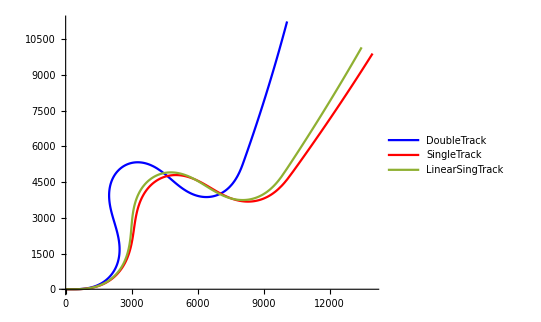

```mathematica
ParametricPlot[{
{xD[t],yD[t]},{xS[t],yS[t]},{xL[t],yL[t]}},{t,0,tf},AspectRatio->Automatic,PlotRange->All,
AspectRatio->Automatic,PlotLegends->{"DoubleTrack","SingleTrack","LinearSingTrack"},
PlotStyle->{Blue,Red,green}]
```

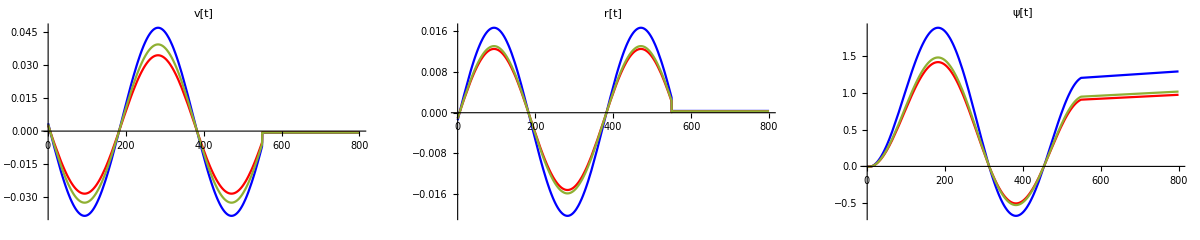

```mathematica
GraphicsRow[{
Plot[{vD[t],vS[t],vL[t]},{t,1,tf},PlotLabel->"v[t]",PlotStyle->{Blue,Red,green}],
Plot[{rD[t],rS[t],rL[t]},{t,1,tf},PlotLabel->"r[t]",PlotStyle->{Blue,Red,green}],
Plot[{ψD[t],ψS[t],ψL[t]},{t,1,tf},PlotLabel->"ψ[t]",PlotStyle->{Blue,Red,green}]},
ImageSize->1200,Frame->True,PlotLabel->"Comparison of Double, Single and Linear Single Track Model"]
```